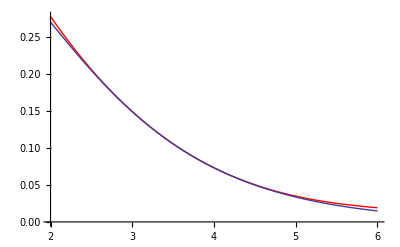

The Taylor expansion is g(x) = 0.105691-0.0754935 (-3.5+x)+0.022648 (-3.5+x)^2-0.00251645 (-3.5+x)^3

Norm error is 0.0000169451

Mean norm error is 4.23628×10^-6

System of equations matrix for p(x) is (1 | 2. | 4. | 8.
1 | 3. | 9. | 27.
1 | 4. | 16. | 64.
1 | 5. | 25. | 125.)

Solutions matrix for p(x) is (0.270671
0.149361
0.0732626
0.0336897)

The coefficient matrix for p(x) is (0.683661
-0.271971
0.0356327
-0.00144748)

The polynomial p(x) = 0.683661-0.271971 x+0.0356327 x^2-0.00144748 x^3

Plotting the polynomial interpretation p(x) (in green) along with f(x) and Talyor expansion (in red).

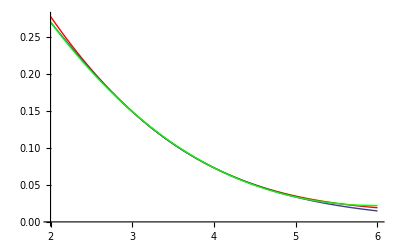

```mathematica
Clear [x,a]
a=3.5;
f[x_]:=x*Exp[-x];
deriv[x_]:=Evaluate[D[f[x],x]];
deriv2[x_]:=Evaluate[D[f[x],x,x]];
deriv3[x_]:=Evaluate[D[f[x],x,x,x]];
g[x_]:=f[a]+deriv[a]*(x-a)+1/(2!)*deriv2[a]*(x-a)^2+1/(3!)*deriv3[a]*(x-a)^3;
gPlot = Plot[g[x],{x,2,6},PlotStyle->{Red}];
fPlot  = Plot[f[x],{x,2,6}];
Show[gPlot,fPlot]
error1 = ∫_2^6 (f[x]-g[x])^2 ⅆx;
Print["The Taylor expansion is g(x) = ", g[x]]
Print["Norm error is ",error1]
Print["Mean norm error is ", 1/4*error1]
Subscript[x, 1]=2.;
Subscript[x, 2]=3.;
Subscript[x, 3]=4.;
Subscript[x, 4]=5.;
X1={{Subscript[x, 1]^0,Subscript[x, 1]^1,Subscript[x, 1]^2,Subscript[x, 1]^3}, {Subscript[x, 2]^0,Subscript[x, 2]^1,Subscript[x, 2]^2,Subscript[x, 2]^3},{Subscript[x, 3]^0,Subscript[x, 3]^1,Subscript[x, 3]^2,Subscript[x, 3]^3},{Subscript[x, 4]^0,Subscript[x, 4]^1,Subscript[x, 4]^2,Subscript[x, 4]^3}};
Print["System of equations matrix for p(x) is ",MatrixForm[X1]]
Y ={f[Subscript[x, 1]],f[Subscript[x, 2]],f[Subscript[x, 3]],f[Subscript[x, 4]]};
Print["Solutions matrix for p(x) is ",MatrixForm[Y]]
Print["The coefficient matrix for p(x) is ",MatrixForm[LinearSolve[X1,Y]]]
p[x_]:=.683661 - .271971x + .0356327 x^2 - .00144748 x^3;
interPlot=Plot[p[x],{x,2,6},PlotStyle-> {Green}];
Print["The polynomial p(x) = ",p[x]]
Print["Plotting the polynomial interpretation p(x) (in green) along with f(x) and Talyor expansion (in red)."]
Show[gPlot,fPlot,interPlot]
```